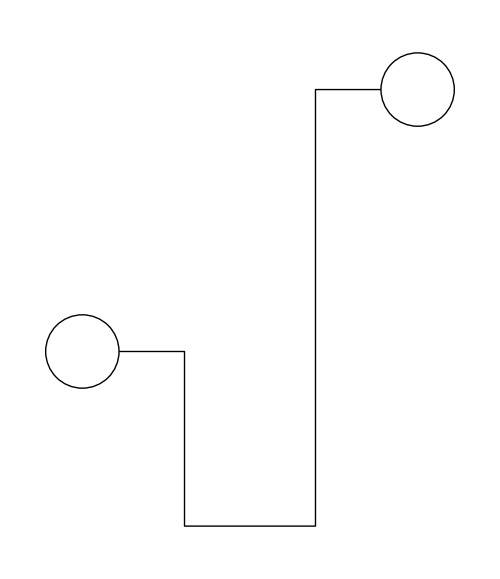

```mathematica
Module[{r0,r1,x1,y1},
r0=0.07;r1=0.1;
x1=0.25;y1=1;

Graphics[{
Circle[{-r0,0},r0],Circle[{2*x1+r0,0.5*y1},r0],
Line[{{0,0},{x1/2,0},{x1/2,-y1/3},{1.5*x1,-y1/3},{1.5*x1,0.5*y1},{2*x1,0.5*y1}}]
},ImageSize->500]
]
```

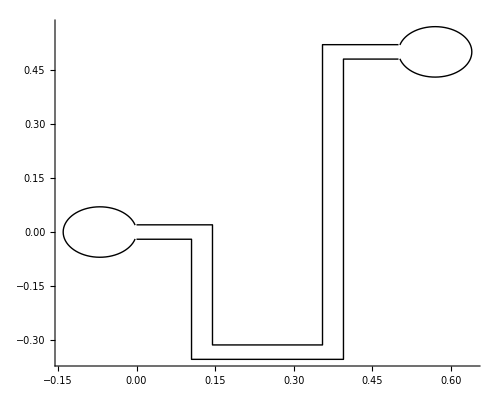

```mathematica
Module[{r0,r1,x1,y1,θ1},
r0=0.07;r1=0.02;
x1=0.25;y1=1;
θ1=ArcTan[r1/r0];

Graphics[{Thick,
Circle[{-r0,0},r0,{θ1,2*π-θ1}],Circle[{2*x1+r0,0.5*y1},r0,{π+θ1,3*π-θ1}],
Line[{{0,0+#},{x1/2+#,0+#},{x1/2+#,-y1/3+#},{1.5*x1-#,-y1/3+#},{1.5*x1-#,y1/2+#},{2*x1,y1/2+#}}]&/@{-r1,r1}
},ImageSize->{500,400},Axes->True]
]
```

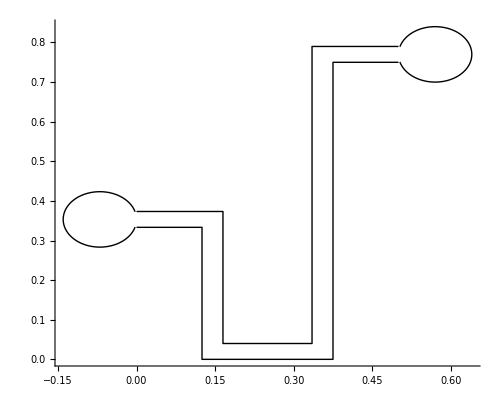

```mathematica
Module[{r0,r1,x1,y1,θ1},
r0=0.07;r1=0.04;
x1=0.25;y1=1;
θ1=ArcTan[0.5*r1/r0];

Graphics[{Thick,
Circle[{-r0,y1/3+r1/2},r0,{θ1,2*π-θ1}],Circle[{2*x1+r0,0.75*y1+r1/2},r0,{π+θ1,3*π-θ1}],
Line[{{0,y1/3+#},{x1/2+#,y1/3+#},{x1/2+#,#},{1.5*x1-#,#},{1.5*x1-#,3/4*y1+#},{2*x1,3/4*y1+#}}]&/@{0,r1}
},ImageSize->{500,400},Axes->True]
]
```

```mathematica
Manipulate[
Module[{r0,r1,x1,y1,θ1,h1},
r0=0.07;r1=0.04;x1=0.25;y1=1;θ1=ArcTan[0.5*r1/r0];

h1=hL1*y1/2;

Graphics[{Thick,
Circle[{-r0,y1/2+r1/2},r0,{θ1,2*π-θ1}],Circle[{2.5*x1+r0,y1+r1/2},r0,{π+θ1,3*π-θ1}],
Line[{{0,y1/2+#},{x1/2+#,y1/2+#},{x1/2+#,#},{2*x1-#,#},{2*x1-#,y1+#},{2.5*x1,y1+#}}]&/@{0,r1},

(*{EdgeForm@Thick,FaceForm@Cyan,FilledCurve[{{x1/2+#,h1+#},{x1/2+#,#},{2*x1-#,#},{2*x1-#,y1+#}}&/@{0,r1}]}*)
(*Red,Line[{{x1/2+#,h1},{x1/2+#,#},{2*x1-#,#},{2*x1-#,y1}}&/@{0,r1}]*)
(*Red,FilledCurve[Line[{{x1/2+#,h1},{x1/2+#,#},{2*x1-#,#},{2*x1-#,y1}}]&/@{0,r1}]*)
(*{#2,Line[{{x1/2+#1,h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,y1}}]}&@@@{{0,Red},{r1,Blue}}*)
(*{#2,Line[{{x1/2+If[#1==0,r1,0],h1},{x1/2+If[#1==0,0,r1],h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,y1}}]}&@@@{{0,Red},{r1,Blue}}*)
(*{If[#1==r1,Dashed,Thick],#2,Line[{{x1/2,h1},{x1/2+r1,h1},{x1/2+#1,h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,y1},{2*x1,y1},{2*x1-r1,y1}}]}&@@@{{0,Red},{r1,Blue}}*)
(*Red,FilledCurve[Line[{(*{x1/2,h1},*){x1/2+r1,h1},{x1/2+#1,h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,y1},{2*x1,y1}(*,{2*x1-r1,y1}*)}]&/@{0,r1}]*)
(*EdgeForm@Thick,FaceForm@*)Cyan,FilledCurve[Line[{{x1/2+r1,h1},{x1/2+#1,h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,y1},{2*x1,y1}}]&/@{0,r1}]
},ImageSize->{500,400},Axes->True]
],
Control[{{hL1,0.6,"height of liquid 1"},0.1,0.9,0.01,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{r0,r1,x1,y1,θ1,h1,h2},
r0=0.07;r1=0.04;x1=0.25;y1=1;θ1=ArcTan[0.5*r1/r0];

h1=hL1*y1/2;h2=hL2*y1;

Graphics[{Thick,
{Cyan,FilledCurve[Line[{{x1/2+r1,h1},{x1/2+#1,h1},{x1/2+#1,#1},{2*x1-#1,#1},{2*x1-#1,h2},{2*x1,h2}}]&/@{0,r1}]},

Circle[{-r0,y1/2+r1/2},r0,{θ1,2*π-θ1}],Circle[{2.5*x1+r0,y1+r1/2},r0,{π+θ1,3*π-θ1}],
Line[{{0,y1/2+#},{x1/2+#,y1/2+#},{x1/2+#,#},{2*x1-#,#},{2*x1-#,y1+#},{2.5*x1,y1+#}}]&/@{0,r1},
},ImageSize->{500,400},Axes->True]
],
Control[{{hL1,0.6,"height of liquid 1"},0.1,0.9,0.01,Appearance->"Labeled"}],
Control[{{hL2,0.8,"height of liquid 2"},0.1,0.9,0.01,Appearance->"Labeled"}]
]
```